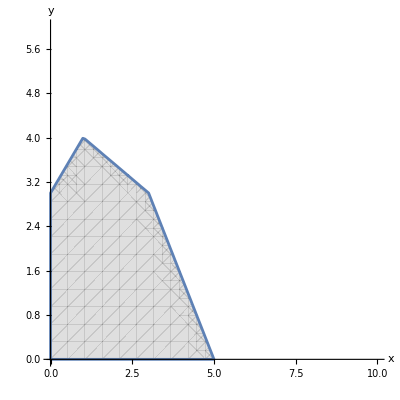

```mathematica
(*
Задача 1. Решете задачата на линейното програмиране
F(x,y)=3y−x->max(min)
Ω е областта съставена от
|-x+y-3<=0
|-x-2y+9>=0
|3x+2y-15<=0
|x>=0
|y>=0

*)

(* 1. Скицирайте областта Ω. *)

p = RegionPlot[
-x+y-3<=0 && 
-x-2*y+9>=0 && 
3*x+2*y-15<=0&&
x>=0&&
y>=0,
{x,0,10},
{y,0,6},
Axes->True,
Frame->False,
AxesLabel->{x,y},
PlotStyle->{Directive[Gray,Opacity[0.25]]}
]
```

```mathematica
(* Множеството на всички производствени планове е петоъгълник *)
```

```mathematica
(* 2. Намерете върховете на Ω и ги скицирайте. *)

(* 
	Трябва да намерим екстремалните точки.
  За целта трябва да изчислим координатите на върховете.
*)

(* Определяме първия връх *)
Reduce[-x+y-3==0&&x==0,{x,y}]
```

x==0&&y==3

```mathematica
a1= {0,3}
```

{0,3}

```mathematica
(* Определяме втория връх *)
```

```mathematica
Reduce[-x+y-3==0&&-x-2*y+9==0,{x,y}]
```

x==1&&y==4

```mathematica
a2={1, 4}
```

{1,4}

```mathematica
(* Определяме третия връх *)
```

```mathematica
Reduce[-x-2*y+9==0&&3*x+2*y-15==0, {x,y}]
```

x==3&&y==3

```mathematica
a3={3, 3}
```

{3,3}

```mathematica
(* Определяме четвъртия връх *)
```

```mathematica
Reduce[y==0&&3*x+2*y-15==0, {x, y}]
```

x==5&&y==0

```mathematica
a4={5, 0}
```

{5,0}

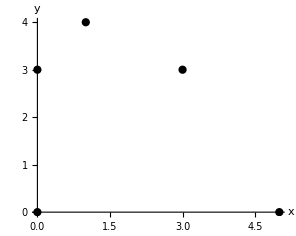

```mathematica
(* Скицираме върховете на Ω *)
t=Graphics[
{Black, PointSize[.02], Point[{{0,0}, a1,a2,a3,a4}]},
AxesOrigin->{0,0}, Axes->True, AxesLabel->{x,y}
]
```

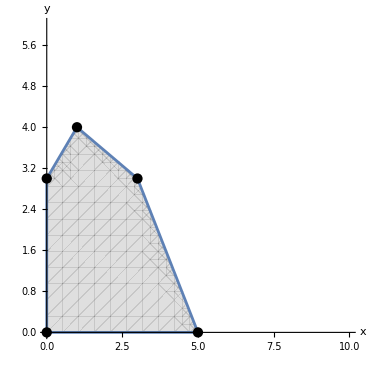

```mathematica
r1=Show[p,t]
```

```mathematica
(* Функцията от условието: *)
F[x_,y_]=-x+3y
```

-x+3 y

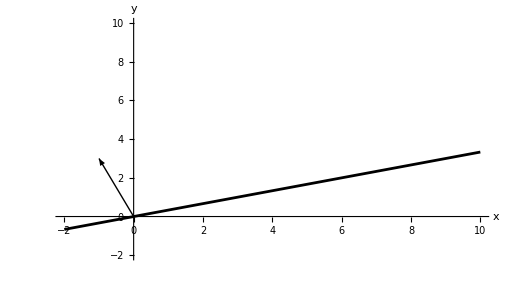

```mathematica
(* 
3. За функцията F(x1,x2) скицирайте производствените планове {x1,x2}, при които F(x1,x2)=0. 
На същия чертеж скицирайте векторът,показващ направлението в което нараства F(x1,x2).
*)

g0=ContourPlot[
F[x,y]==0,
{x, -2, 10},
{y, -2, 10},
Axes->True,
Frame->False,
AxesLabel->{x,y},
ContourStyle->{Directive[Black]},
AspectRatio->Automatic,
Epilog->{Arrow[{{0,0}, {-1,3}}]}
]
```

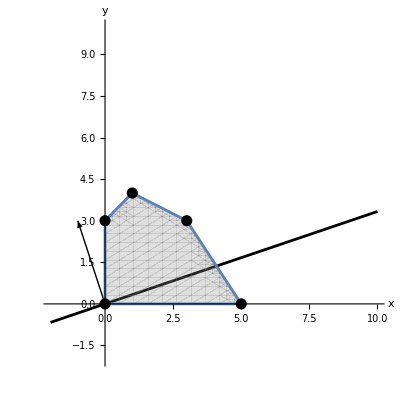

```mathematica
Show[g0, r1]
```

```mathematica
(* 4.Направете анимация за откриване на оптималните решения. *)
animatedPlot[s_]:=ContourPlot[
F[x,y]== s,
{x, -2,10},
{y, -2, 10},
Axes->True,
Frame->False,
ContourStyle->{Directive[Black]},
AxesLabel->{x,y},
AspectRatio->Automatic
]
```

```mathematica
Animate[Show[g0,animatedPlot[s],p,t],{s,-10,20},AnimationRunning->False]
```

```mathematica
(* Тоест минимумът и максимумът се получават върху поне един от върховете *)
```

```mathematica
{a1, a2, a3, a4}
```

{{0,3},{1,4},{3,3},{5,0}}

```mathematica
allPoints = {{0,0}, a1, a2, a3, a4}
```

{{0,0},{0,3},{1,4},{3,3},{5,0}}

```mathematica
M={
F[allPoints[[1, 1]], allPoints[[1,2]]],
F[allPoints[[2, 1]], allPoints[[2,2]]],
F[allPoints[[3, 1]], allPoints[[3,2]]],
F[allPoints[[4, 1]], allPoints[[4,2]]],
F[allPoints[[5, 1]], allPoints[[5,2]]]
}
```

{0,9,11,6,-5}

```mathematica
ourMax= Max[M]
(* Максът е в точката {1,4}*)
```

11

```mathematica
ourMin=Min[M]
(* Минимумът е в точката {5,0}*)
```

-5

```mathematica
(* 6. Решете задачата с функцията LinearProgramming[...]. *)
```

```mathematica
F[x_,y_]
```

-x_+3 y_

```mathematica
(* Макс и мин *)
```

```mathematica
c={-1,3}
```

{-1,3}

```mathematica
m=({{-1, 1}, {1, 2}, {3, 2}})
```

{{-1,1},{1,2},{3,2}}

```mathematica
b=({{3, -1}, {9, -1}, {15, -1}})
```

{{3,-1},{9,-1},{15,-1}}

```mathematica
v=LinearProgramming[c, m, b]
```

{5,0}

```mathematica
(* Планът с x=5 и y=0 е минимум и минималната печалба на F[x,y] е *)
```

```mathematica
F[5,0]
```

-5

```mathematica
(* Понеже LinearProgramming е само за минимизация, то трябва да обърнем целевата фунцкия *)
```

```mathematica
cReversed = {1,-3}
```

{1,-3}

```mathematica
vv=LinearProgramming[cReversed, m, b]
```

{1,4}

```mathematica
(* => максималната стойност на функцията е: *)
```

```mathematica
maxValue=-cReversed.vv
```

11

```mathematica
(* доказателство *)
```

```mathematica
F[1,4]
```

11

```mathematica
(* 7. Намерете всички решения и ги скицирайте. *)
(* Решенията на целевата фунцкия ги имаме във вектора M *)
M
```

{0,9,11,6,-5}

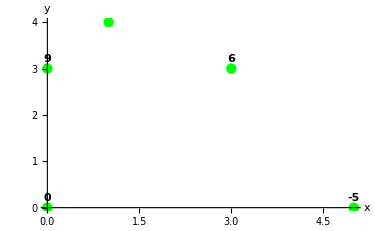

```mathematica
lp = ListPlot[
allPoints,
PlotStyle->Directive[PointSize[.02],Green],
AxesLabel->{x,y},
Epilog->{Table[Text[Style[M[[i]],Black,Bold],allPoints[[i]]+{0.0, 0.2}],{i,1,Length[allPoints]}]}]
```

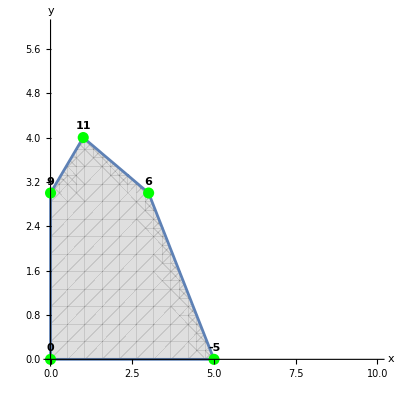

```mathematica
Show[p, lp, Epilog->{Table[Text[Style[M[[i]],Black,Bold],allPoints[[i]]+{0.0, 0.2}],{i,1,Length[allPoints]}]}]
```

```mathematica
(* 8. Решение на задачата с функциите Reduce[...] и Maximize[...]. *)
F[x_, y_]=-x+3*y
```

-x+3 y

```mathematica
Reduce[3y−x==11&&−x+y−3≤0&&−x−2y+9≥0&&3x+2y−15≤0&&x≥0&&y≥0,{x,y}]
```

x==1&&y==4

```mathematica
x==1&&y==4
(* оптимален план *)
```

x==1&&y==4

```mathematica
Maximize[{F[x,y],−x+y−3≤0&&−x−2y+9≥0&&3x+2y−15≤0&&x≥0&&y≥0},{x,y}]
```

{11,{x→1,y→4}}